```mathematica
Acap =True;
Bcap = True;

simulatedVoltagesPath = "C:\\Users\\Nelson's Laptop\\OneDrive - Universität Zürich UZH\\University\\Master\\LTSpice\\Data\\Single_Layer_Simulation\\";
importedVoltages = Import[#,"Table"]&/@(FileNames[simulatedVoltagesPath<>Which[Acap==True && Bcap==True,"\\AB_cap_",Acap==True,"\\A_cap_",Bcap==True,"\\B_cap_",True,"\\no_cap_"]<>"eti_*.txt"]);

measuredVoltagesPath = "C:\\Users\\Nelson's Laptop\\OneDrive - Universität Zürich UZH\\University\\Master\\MLA Data\\Board_2_Complete_Measurement_Inputs_(4,4,2)_221107\\";
measuredVoltages = Import[#,"Table"]&/@(FileNames[measuredVoltagesPath<>"\\Voltages_*.txt"]);
```

```mathematica
Sandwich = True;
hermitian = True;

NUnit = 8;

systemLengthX = NUnit;
systemLengthY = NUnit;
systemLengthZ = 1;


p1=Flatten[Table[{{5-p,5-q,1,2},{5-p,5-q,1,1}},{p,1,4},{q,1,4}],2];
p2=Flatten[Table[{{9-p,5-q,1,2},{9-p,5-q,1,1}},{p,1,4},{q,1,4}],2];
p3=Flatten[Table[{{4+p,4+q,1,1},{4+p,4+q,1,2}},{p,1,4},{q,1,4}],2];
p4=Flatten[Table[{{p,4+q,1,1},{p,4+q,1,2}},{p,1,4},{q,1,4}],2];

coordConvention=Join[p1,p2,p3,p4];

reorderingPos = {Flatten[Table[Position[coordConvention,{x,y,1,1}][[1,1]],{x,1,8},{y,1,8}],1],Flatten[Table[Position[coordConvention,{x,y,1,2}][[1,1]],{x,1,NUnit},{y,1,NUnit}],1]};
```

```mathematica
appliedVoltage = 0.25;
RShunt = 10;

L1Value = 27*10^-6;
L2Value = 5.6*10^-6;
L3Value = 27*10^-6;

C1Value = 150*10^-12;
C2Value = 75*10^-12;
C3Value = 150*10^-12;

Ry = 15.92;


ltSpiceFreq = -51;

frequency = 2.5*10^6;


inputRow =4;
inputColumn = 4;
inputHeight = 1;

InputNodes ={{inputRow,inputColumn,inputHeight,1},{inputRow,inputColumn,inputHeight,2}};

inputPos ={Position[coordConvention,{inputRow,inputColumn,1,1}][[1,1]],Position[coordConvention,{inputRow,inputColumn,1,2}][[1,1]]};
```

```mathematica
circuitGroundMatrixFourier = Table[Which[x==y,Which[coordConvention[[x,4]]==1,(I*driveFreq*L2Value)^-1+If[Sandwich==True && Acap==True,I*driveFreq*C1Value,0],coordConvention[[x,4]]==2,(I*driveFreq*L3Value)^-1+If[Sandwich==True && Bcap==True,I*driveFreq*C1Value,0],True,0],True,0],{x,1,Length[coordConvention]},{y,1,Length[coordConvention]}];

adjacencyMatrixXToYSameCellFourier= Table[Which[
coordConvention[[x]]==coordConvention[[y]]-{0,0,0,1}||
coordConvention[[x]]==coordConvention[[y]]+{0,0,0,1},I*driveFreq*C1Value,
True,0],{x,1,Length[coordConvention]},{y,1,Length[coordConvention]}];
 
adjacencyMatrixXToYDifferentCellFourier = Table[Which[
coordConvention[[x]]==Mod[coordConvention[[y]]+{-1,1,0,1},8,1] ||
coordConvention[[x]]==Mod[coordConvention[[y]]-{-1,1,0,1},8,1] ||
coordConvention[[x]]==Mod[coordConvention[[y]]+{1,-1,0,1},8,1]||
coordConvention[[x]]==Mod[coordConvention[[y]]-{1,-1,0,1},8,1] ,I*driveFreq*C2Value,
True,0],{x,1,Length[coordConvention]},{y,1,Length[coordConvention]}];

adjacencyMatrixXToXFourier = Table[Which[
coordConvention[[x]]==Mod[coordConvention[[y]]+{0,1,0,0},8,1] ||
coordConvention[[x]]==Mod[coordConvention[[y]]-{0,1,0,0} ,8,1]
,Which[
coordConvention[[x,4]]==1,I*driveFreq*C3Value,
coordConvention[[x,4]]==2,(I*driveFreq*L1Value)^-1,
coordConvention[[x]]==Mod[coordConvention[[y]]+{1,0,0,0},8,1] ||
coordConvention[[x]]==Mod[coordConvention[[y]]-{1,0,0,0} ,8,1]
,If[hermitian==False,Ry^-1,0],
True,0],True,0],{x,1,Length[coordConvention]},{y,1,Length[coordConvention]}];


totalNodeConductanceMatrixFourier = Table[Which[x==y,Which[coordConvention[[x,4]]==1,I*driveFreq*C1Value+2*I*driveFreq*C3Value+2*I*driveFreq*C2Value+If[hermitian==False,2 Ry^-1,0],coordConvention[[x,4]]==2,I*driveFreq*C1Value+2*I*driveFreq*C2Value+2*(I*driveFreq*L1Value)^-1+If[hermitian==False,2 Ry^-1,0]
,True,0],True,0],{x,1,Length[coordConvention]},{y,1,Length[coordConvention]}];
```

```mathematica
testLap = totalNodeConductanceMatrixFourier-(adjacencyMatrixXToXFourier+adjacencyMatrixXToYDifferentCellFourier+adjacencyMatrixXToYSameCellFourier)+circuitGroundMatrixFourier;
```

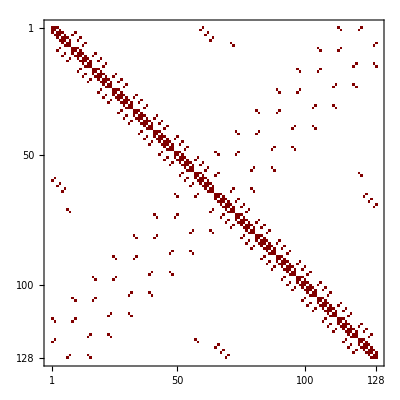

```mathematica
testLap//MatrixPlot
```

```mathematica
x=128;
y=1;

coordConvention[[x]]
coordConvention[[y]]

testLap[[x,y]]



Clear[x,y]
```

{4,8,1,2}

{4,4,1,2}

0

```mathematica
laplacianMatrixFourier[ω_]:= ReplaceAll[totalNodeConductanceMatrixFourier-(adjacencyMatrixXToXFourier+adjacencyMatrixXToYDifferentCellFourier+adjacencyMatrixXToYSameCellFourier)+circuitGroundMatrixFourier,driveFreq->ω];

inverseLaplacianMatrixFourier[ω_]:= Inverse[laplacianMatrixFourier[ω]];

currentVectorCosSubA = Table[If[coordConvention[[node]]==InputNodes[[1]],appliedVoltage/(50+inverseLaplacianMatrixFourier[2π*frequency][[inputPos[[1]],inputPos[[1]]]]),0],{node, 1,Length[coordConvention]}];
currentVectorCosSubB = Table[If[coordConvention[[node]]==InputNodes[[2]],appliedVoltage/(50+inverseLaplacianMatrixFourier[2π*frequency][[inputPos[[2]],inputPos[[2]]]]),0],{node, 1,Length[coordConvention]}];
```

```mathematica
voltageVectorCos = {Dot[currentVectorCosSubA,inverseLaplacianMatrixFourier[2π*frequency]],Dot[currentVectorCosSubB,inverseLaplacianMatrixFourier[2π*frequency]]};

importedVoltagesOrdered = Table[Block[{reIm = ToExpression[StringReplace[StringSplit[importedVoltages[[subInput,ltSpiceFreq,1+sub;;;;2]][[node]],","],"e"->"*10^"]]},Abs[reIm[[1]]+I*reIm[[2]]]*Exp[I*Arg[reIm[[1]]+I*reIm[[2]]]]],{subInput,1,2},{sub,1,2},{node,1,64}];
```

```mathematica
currentsSimImported = Table[Block[{reIm = ToExpression[StringReplace[StringSplit[importedVoltages[[sub,ltSpiceFreq,-1]],","],"e"->"*10^"]]},Abs[reIm[[1]]+I*reIm[[2]]]*Exp[I*Arg[reIm[[1]]+I*reIm[[2]]]]],{sub,1,2}];

voltagesSimulatedOrdered = Table[voltageVectorCos[[subInput,reorderingPos[[sub,node]]]],{subInput,1,2},{sub,1,2},{node,1,64}];

currentVectorSimulatedOrdered =Table[If[reorderingPos[[sub,node]]==inputPos[[sub]],appliedVoltage/(50+inverseLaplacianMatrixFourier[2π*frequency][[sub,sub]]),0],{sub,1,2},{node,1,64}];

currentVectorSimImported =Table[If[reorderingPos[[sub,node]]==inputPos[[sub]],currentsSimImported[[sub]],0],{sub,1,2},{node,1,64}];
```

```mathematica
fourierVoltagesV1 = Table[∑_(l=1)^NUnit ( ∑_(j=1)^NUnit voltagesSimulatedOrdered[[subInput,sub,((j-1)*NUnit)+l]]*Exp[-ⅈ*2*π*kx*j/NUnit])*Exp[-ⅈ*2*π*ky*l/NUnit],{subInput,1,2},{sub,1,2},{kx,1,NUnit},{ky,1,NUnit}];

fourierVoltagesSimImported = Table[∑_(l=1)^NUnit ( ∑_(j=1)^NUnit importedVoltagesOrdered[[subInput,sub,((j-1)*NUnit)+l]]*Exp[-ⅈ*2*π*kx*j/NUnit])*Exp[-ⅈ*2*π*ky*l/NUnit],{subInput,1,2},{sub,1,2},{kx,1,NUnit},{ky,1,NUnit}];

fourierCurrentVector = Table[∑_(l=1)^NUnit ( ∑_(j=1)^NUnit currentVectorSimulatedOrdered[[sub,((j-1)*NUnit)+l]]*Exp[-ⅈ*2*π*kx*j/NUnit])*Exp[-ⅈ*2*π*ky*l/NUnit],{sub,1,2},{kx,1,NUnit},{ky,1,NUnit}];

fourierCurrentVectorSimImported = Table[∑_(l=1)^NUnit ( ∑_(j=1)^NUnit currentVectorSimImported[[sub,((j-1)*NUnit)+l]]*Exp[-ⅈ*2*π*kx*j/NUnit])*Exp[-ⅈ*2*π*ky*l/NUnit],{sub,1,2},{kx,1,NUnit},{ky,1,NUnit}];
```

```mathematica
Detk=Table[ (fourierVoltagesV1[[1,1,kx,ky]]*fourierVoltagesV1[[2,2,kx,ky]])/(fourierCurrentVector[[1,kx,ky]]*fourierCurrentVector[[2,kx,ky]])-(fourierVoltagesV1[[1,2,kx,ky]]*fourierVoltagesV1[[2,1,kx,ky]])/(fourierCurrentVector[[1,kx,ky]]*fourierCurrentVector[[2,kx,ky]]),{kx,1,NUnit},{ky,1,NUnit}];

Lap = Table[1/Detk[[kx,ky]]*{{fourierVoltagesV1[[2,2,kx,ky]]/fourierCurrentVector[[2,kx,ky]],-fourierVoltagesV1[[2,1,kx,ky]]/fourierCurrentVector[[2,kx,ky]]},{-fourierVoltagesV1[[1,2,kx,ky]]/fourierCurrentVector[[1,kx,ky]],fourierVoltagesV1[[1,1,kx,ky]]/fourierCurrentVector[[1,kx,ky]]}},{kx,1,NUnit},{ky,1,NUnit}];

DetkSimImported=Table[ (fourierVoltagesSimImported[[1,1,kx,ky]]*fourierVoltagesSimImported[[2,2,kx,ky]])/(fourierCurrentVectorSimImported[[1,kx,ky]]*fourierCurrentVectorSimImported[[2,kx,ky]])-(fourierVoltagesSimImported[[1,2,kx,ky]]*fourierVoltagesSimImported[[2,1,kx,ky]])/(fourierCurrentVectorSimImported[[1,kx,ky]]*fourierCurrentVectorSimImported[[2,kx,ky]]),{kx,1,NUnit},{ky,1,NUnit}];

LapSimImported = Table[1/DetkSimImported[[kx,ky]]*{{fourierVoltagesSimImported[[2,2,kx,ky]]/fourierCurrentVectorSimImported[[2,kx,ky]],-fourierVoltagesSimImported[[2,1,kx,ky]]/fourierCurrentVectorSimImported[[2,kx,ky]]},{-fourierVoltagesSimImported[[1,2,kx,ky]]/fourierCurrentVectorSimImported[[1,kx,ky]],fourierVoltagesSimImported[[1,1,kx,ky]]/fourierCurrentVectorSimImported[[1,kx,ky]]}},{kx,1,NUnit},{ky,1,NUnit}];
```

```mathematica
jMatrix[kx_,ky_]:= {{C1Value+2C2Value+2C3Value,0},{0,C1Value+2C2Value-2/((2π*frequency)^2 L1Value)}}-{{2*C3Value*Cos[ky],C1Value+2C2Value*Cos[ky-kx]},{C1Value+2C2Value*Cos[ky-kx],-2/((2π*frequency)^2*L1Value)Cos[ky]}}+{{If[Sandwich==True && Acap==True,C1Value,0]-1/((2π*frequency)^2 L2Value),0},{0,If[Sandwich==True && Bcap==True,C1Value,0]-1/((2π*frequency)^2 L3Value)}};

data = Table[SortBy[Eigenvalues[jMatrix[kx,ky]],Im],{kx,0,2π,2π/NUnit},{ky,0,2π,2π/NUnit}];
```

```mathematica
viewpoint = Back;

kTicks = Table[{k,(k-1)(2π)/NUnit},{k,1,8}];

LapEigenvalues = Im[Table[SortBy[Eigenvalues[Lap[[kx,ky]]],Im],{kx,1,NUnit},{ky,1,NUnit}]];

LapEigenvaluesSimImported = Im[Table[SortBy[Eigenvalues[LapSimImported[[kx,ky]]],Im],{kx,1,NUnit},{ky,1,NUnit}]];

ListPlot3D[Transpose[LapEigenvalues,{3,2,1}],AxesLabel->{"ky","kx","Energy"},Ticks->{kTicks,kTicks,Automatic},PlotRange->All,ImageSize->Large,PlotLabel->"Mathematica Simulated Single Layer",ViewPoint->viewpoint]

ListPlot3D[Transpose[LapEigenvaluesSimImported,{3,2,1}],AxesLabel->{"ky","kx","Energy"},Ticks->{kTicks,kTicks,Automatic},PlotRange->All,ImageSize->Large,PlotLabel->"LTSpice Simulated Single Layer",ViewPoint->viewpoint]

ListPlot3D[Transpose[data,{3,2,1}],AxesLabel->{"ky","kx","Energy"},Ticks->{kTicks,kTicks,Automatic},PlotRange->All,ImageSize->Large,PlotLabel->"Theoretical Single Layer",ViewPoint->viewpoint]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
absImpedance[f_,{x_,y_,z_,sub_}]:= Block[{position=Position[coordConvention,{x,y,z,Which[sub==A,1,sub==B,2,True,0]}][[1,1]]},Abs[inverseLaplacianMatrixFourier[2π*f][[position,position]]]];

argImpedance[f_,{x_,y_,z_,sub_}]:= Block[{position=Position[coordConvention,{x,y,z,Which[sub==A,1,sub==B,2,True,0]}][[1,1]]},Arg[inverseLaplacianMatrixFourier[2π*f][[position,position]]]];
```

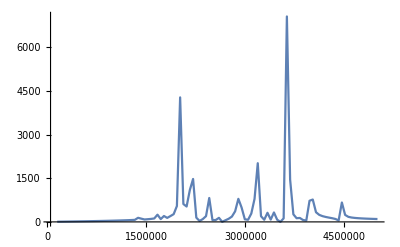

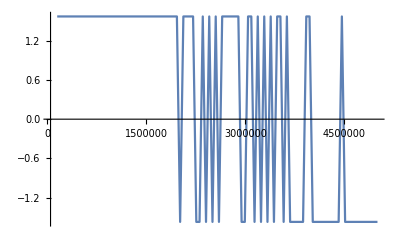

```mathematica
impedanceNode = {4,1,1,A};
maxFreq = 5*10^6;
steps = 100;

absImpedanceValues = Table[{10^5+iterator*(maxFreq-10^5)/steps,absImpedance[10^5+iterator*(maxFreq-10^5)/steps,impedanceNode]},{iterator,1,steps}];

argImpedanceValues = Table[{10^5+iterator*(maxFreq-10^5)/steps,argImpedance[10^5+iterator*(maxFreq-10^5)/steps,impedanceNode]},{iterator,1,steps}];

ListLinePlot[absImpedanceValues,PlotRange->All]
ListLinePlot[argImpedanceValues,PlotRange->All]
```

```mathematica
invertedLaplacian = inverseLaplacianMatrixFourier[2*π*2.5*10^6];
```

```mathematica
laplacianMatrixFourier[2*π*2.5*10^6]//Eigensystem
```

{{8.67362×10^-19+0.00701705 ⅈ,8.67362×10^-19+0.006725 ⅈ,2.1684×10^-19-0.00661257 ⅈ,1.73471×10^-18+0.00655942 ⅈ,-8.56139×10^-19+0.00655942 ⅈ,118,0.-0.000517132 ⅈ,7.58942×10^-19+0.000412762 ⅈ,-2.71051×10^-20+0.000412762 ⅈ,-1.82112×10^-19-4.96956×10^-6 ⅈ,1.19491×10^-18-4.96956×10^-6 ⅈ},{{1},126,{1}}}
 |  |  |  |

```mathematica
inputValues = {0.0026585388963521655+0.0002615716921686406 ⅈ,0.0024380098788940392+0.0007765094180627827 ⅈ};

voltagesV1=Table[(measuredVoltages[[1,reorderingPos[[sub,node]]+2+(2-subInput)*130,2]])*Exp[I*measuredVoltages[[1,reorderingPos[[sub,node]]+2+(2-subInput)*130,3]]],{subInput,1,2},{sub,1,2},{node,1,64}];

voltagesV2=Table[(measuredVoltages[[1,reorderingPos[[sub,node]]+2+(2-subInput)*130,4]])*Exp[I*measuredVoltages[[1,reorderingPos[[sub,node]]+2+(2-subInput)*130,5]]],{subInput,1,2},{sub,1,2},{node,1,64}];

currentVector =Table[If[reorderingPos[[sub,node]]==inputPos[[sub]],inputValues[[sub]],0],{sub,1,2},{node,1,64}];
```

```mathematica
renorm = (Abs[voltagesV2[[1,1,inputPos[[1]]]]])/(Abs[voltagesSimulatedOrdered[[1,1,inputPos[[1]]]]]);

normMeasToSimDeviation =Table[(voltagesV2[[subInput,sub,((j-1)*NUnit)+l]]/renorm - voltagesSimulatedOrdered[[subInput,sub,((j-1)*NUnit)+l]]),{subInput,1,2},{sub,1,2},{j,1,NUnit},{l,1,NUnit}];

normMeasToSimDeviationPercent = Table[(voltagesV2[[subInput,sub,((j-1)*NUnit)+l]]/renorm - voltagesSimulatedOrdered[[subInput,sub,((j-1)*NUnit)+l]])/(Abs[voltagesSimulatedOrdered[[subInput,sub,((j-1)*NUnit)+l]]]),{subInput,1,2},{sub,1,2},{j,1,NUnit},{l,1,NUnit}];
```

```mathematica
voltagesV2[[1,1,1]]
voltagesSimulatedOrdered[[1,1,1]]
Abs[voltagesSimulatedOrdered[[1,1,6]]]
```

-9.52532+17.4722 ⅈ

0.182576-0.143335 ⅈ

0.00616549

```mathematica
Manipulate[MatrixForm[Reverse[Transpose[normMeasToSimDeviation[[subInput,sub]]]]],{subInput,1,2,1},{sub,1,2,1}]
```

Part::partd: Part specification normMeasToSimDeviation⟦1,1⟧ is longer than depth of object.

```mathematica
Manipulate[MatrixForm[Reverse[Im[Transpose[normMeasToSimDeviationPercent[[subInput,sub]]]]]],{subInput,1,2,1},{sub,1,2,1}]
```

Part::partd: Part specification normMeasToSimDeviationPercent⟦1,1⟧ is longer than depth of object.

```mathematica
cellsHistMulti =Table[{i,i},{i,8}];

realDeviationHist = Table[DiscretePlot3D[Abs[Re[normMeasToSimDeviationPercent[[subInput,sub,x,y]]]],{x,1,8},{y,1,8},ExtentSize->Full,FillingStyle->Opacity[0.7],PlotRange->{All,All,{0,Max[Abs[Re[normMeasToSimDeviationPercent[[subInput,sub]]]]]}},TicksStyle->White,Ticks->{cellsHistMulti,cellsHistMulti,{{0,"0"},{Max[Abs[Re[normMeasToSimDeviationPercent[[subInput,sub]]]]]/2,ToExpression[100*Max[Abs[Re[normMeasToSimDeviationPercent[[subInput,sub]]]]]/2]},{Max[Abs[Re[normMeasToSimDeviationPercent[[subInput,sub]]]]],ToExpression[100*Max[Abs[Re[normMeasToSimDeviationPercent[[subInput,sub]]]]]]}}},ColorFunction->Function[{x,y,z},RGBColor[z^2,0,0]],AxesLabel->{"x-Axis","y-Axis","Deviation in %"},AxesStyle->White,FaceGrids->All,ViewPoint->{-1,-1,1.5},PlotLabel->Style["Deviation from simulation value in % of sublattice "<>ToString[If[sub==1,A,B]]<>" with input sub "<>ToString[If[subInput==1,A,B]],White],ImageSize->400,Background->Black],{subInput,1,2},{sub,1,2}];

imaginaryDeviationHist = Table[DiscretePlot3D[Abs[Im[normMeasToSimDeviationPercent[[subInput,sub,x,y]]]],{x,1,8},{y,1,8},ExtentSize->Full,FillingStyle->Opacity[0.7],PlotRange->{All,All,{0,Max[Abs[Im[normMeasToSimDeviationPercent[[subInput,sub]]]]]}},TicksStyle->White,Ticks->{cellsHistMulti,cellsHistMulti,{{0,"0"},{Max[Abs[Im[normMeasToSimDeviationPercent[[subInput,sub]]]]]/2,ToExpression[100*Max[Abs[Im[normMeasToSimDeviationPercent[[subInput,sub]]]]]/2]},{Max[Abs[Im[normMeasToSimDeviationPercent[[subInput,sub]]]]],ToExpression[100*Max[Abs[Im[normMeasToSimDeviationPercent[[subInput,sub]]]]]]}}},ColorFunction->Function[{x,y,z},RGBColor[z^2,0,0]],AxesLabel->{"x-Axis","y-Axis","Deviation in %"},AxesStyle->White,FaceGrids->All,ViewPoint->{-1,-1,1.5},PlotLabel->Style["Deviation from simulation value in % of sublattice "<>ToString[If[sub==1,A,B]]<>" with input sub "<>ToString[If[subInput==1,A,B]],White],ImageSize->400,Background->Black],{subInput,1,2},{sub,1,2}];
```

```mathematica
Manipulate[realDeviationHist[[subInput,sub]],{subInput,1,2,1},{sub,1,2,1},ControlType->VerticalSlider,SaveDefinitions->True]
```

```mathematica
Manipulate[imaginaryDeviationHist[[subInput,sub]],{subInput,1,2,1},{sub,1,2,1},ControlType->VerticalSlider,SaveDefinitions->True]
```

```mathematica
(8,3),(8,5),(6,5)
```

```mathematica
-Graphics3D--Graphics3D-
-Graphics3D--Graphics3D-
```

-Graphics3D- -Graphics3D-

-Graphics3D- -Graphics3D-

```mathematica
(8,5),(8,7),(6,5),(6,7),(6,1),(6,3),(2,7)
```

```mathematica
-Graphics3D--Graphics3D-
-Graphics3D--Graphics3D-
```

-Graphics3D- -Graphics3D-

-Graphics3D- -Graphics3D-